# CRNSSA Runtime Testing

```mathematica
<<CRNSSA`
```

```mathematica
ConstructSys1[n_,type_]:=Module[
{rxns,xInits,yInits,inits},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xInits=Table[type[x[i],RandomInteger[100]],{i,n}];
yInits=Table[type[y[i],RandomInteger[100]],{i,n}];
inits=Flatten[{xInits,yInits}];
{rxns,inits}]
```

```mathematica
ConstructSys2[n_,type_]:=Module[
{k,rxns,xInits,yInits,inits},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[Plus@@Table[x[i,l]+x[j,l],{l,k}],Plus@@Table[y[i,l]+y[j,l],{l,k}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xInits=Flatten[Table[type[x[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
yInits=Flatten[Table[type[y[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
inits=Flatten[{xInits,yInits}];
{rxns,inits}]
```

```mathematica
ConstructSys3[n_,type_]:=Module[
{rxns,inits},
rxns= Table[revrxn[Plus@@Table[x[j],{j,n}],Plus@@Table[y[j],{j,n}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xInits=Table[type[x[i],RandomInteger[100]],{i,n}];
yInits=Table[type[y[i],RandomInteger[100]],{i,n}];
inits=Flatten[{xInits,yInits}];
{rxns,inits}]
```

```mathematica
TestSys[construction_,algo_,kRange_,iters_,statesOnlyFlag_]:=Module[{type},
If[algo==="Opt",type=init,type=conc];
Table[Module[
{n,rxns,inits,rxnsys,nRxns,nSpecies,results,time,nIters,timePerIter},
n=k^2;
{rxns,inits} = construction[n,type];
rxnsys=Flatten[{rxns,inits}];
nRxns=Length[rxns];
nSpecies=If[algo==="Opt",
Length[GetSpecies[rxnsys]],
Length[SpeciesInRxnsys[rxnsys]]];
results=If[algo==="Opt",
Timing[DirectSSA[rxnsys,useIter->True,iterEnd->iters,statesOnly->statesOnlyFlag,finalOnly->True,outputTS->False]],
Timing[SimulateRxnsysSSA[rxnsys,2/n]]];
time=results[[1]];
nIters=If[algo==="Opt",
iters,
Length[Normal[results[[2]]]]];
timePerIter=time/nIters;
{nRxns,nSpecies,time,nIters,timePerIter}],
kRange]]
```

```mathematica
constructions={ConstructSys1,ConstructSys2,ConstructSys3};
algo="Opt";
kRange={k,{1,10,25,50}};
iters=10000;
statesOnlyFlags={False,True};
resultsOpt=Table[TestSys[constructions[[i]],algo,kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}]
```

{{{{2,2,0.0625,10000,6.25×10^-6},{200,200,0.734375,10000,0.0000734375},{1250,1250,6.6875,10000,0.00066875},{5000,5000,101.234,10000,0.0101234}},{{2,2,0.03125,10000,3.125×10^-6},{200,200,0.46875,10000,0.000046875},{1250,1250,7.15625,10000,0.000715625},{5000,5000,104.281,10000,0.0104281}}},{{{2,2,0.046875,10000,4.6875×10^-6},{200,200,1.34375,10000,0.000134375},{1250,1250,74.5,10000,0.00745},{5000,5000,2089.06,10000,0.208906}},{{2,2,0.09375,10000,9.375×10^-6},{200,200,1.34375,10000,0.000134375},{1250,1250,71.4531,10000,0.00714531},{5000,5000,2097.94,10000,0.209794}}},{{{2,2,0.140625,10000,0.0000140625},{200,200,5.82813,10000,0.000582813},{1250,1250,788.078,10000,0.0788078},{5000,5000,54876.1,10000,5.48761}},{{2,2,1.6875,10000,0.00016875},{200,200,3.92188,10000,0.000392188},{1250,1250,911.25,10000,0.091125},{5000,5000,54126.9,10000,5.41269}}}}

{{{2,6.25×10^-6},{200,0.0000734375},{1250,0.00066875},{5000,0.0101234}},{{2,3.125×10^-6},{200,0.000046875},{1250,0.000715625},{5000,0.0104281}},{{2,4.6875×10^-6},{200,0.000134375},{1250,0.00745},{5000,0.208906}},{{2,9.375×10^-6},{200,0.000134375},{1250,0.00714531},{5000,0.209794}},{{2,0.0000140625},{200,0.000582813},{1250,0.0788078},{5000,5.48761}},{{2,0.00016875},{200,0.000392188},{1250,0.091125},{5000,5.41269}}}

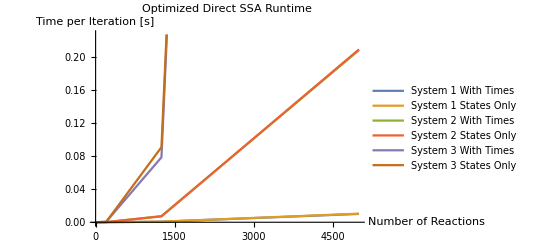

```mathematica
coorsOpt=Flatten[
Table[
Table[{resultsOpt[[i]][[j]][[l]][[1]],resultsOpt[[i]][[j]][[l]][[5]]},{l,Length[resultsOpt[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1]
constructionLabels={"System 1","System 2","System 3"};
statesOnlyLabels={" With Times"," States Only"};
labelsOpt=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],1];
ListLinePlot[coorsOpt,PlotLegends->labelsOpt,AxesLabel->{"Number of Reactions","Time per Iteration [s]"},"PlotLabel"->"Optimized Direct SSA Runtime"]
```

```mathematica
Export["runtimeResults.mx", resultsOpt];
Export["runtimeCoors.mx", coorsOpt];
```

```mathematica
Import["runtimeResults.mx"]
Import["runtimeCoors.mx"]
```

{{{{2,2,0.0625,10000,6.25×10^-6},{200,200,0.734375,10000,0.0000734375},{1250,1250,6.6875,10000,0.00066875},{5000,5000,101.234,10000,0.0101234}},{{2,2,0.03125,10000,3.125×10^-6},{200,200,0.46875,10000,0.000046875},{1250,1250,7.15625,10000,0.000715625},{5000,5000,104.281,10000,0.0104281}}},{{{2,2,0.046875,10000,4.6875×10^-6},{200,200,1.34375,10000,0.000134375},{1250,1250,74.5,10000,0.00745},{5000,5000,2089.06,10000,0.208906}},{{2,2,0.09375,10000,9.375×10^-6},{200,200,1.34375,10000,0.000134375},{1250,1250,71.4531,10000,0.00714531},{5000,5000,2097.94,10000,0.209794}}},{{{2,2,0.140625,10000,0.0000140625},{200,200,5.82813,10000,0.000582813},{1250,1250,788.078,10000,0.0788078},{5000,5000,54876.1,10000,5.48761}},{{2,2,1.6875,10000,0.00016875},{200,200,3.92188,10000,0.000392188},{1250,1250,911.25,10000,0.091125},{5000,5000,54126.9,10000,5.41269}}}}

{{{2,6.25×10^-6},{200,0.0000734375},{1250,0.00066875},{5000,0.0101234}},{{2,3.125×10^-6},{200,0.000046875},{1250,0.000715625},{5000,0.0104281}},{{2,4.6875×10^-6},{200,0.000134375},{1250,0.00745},{5000,0.208906}},{{2,9.375×10^-6},{200,0.000134375},{1250,0.00714531},{5000,0.209794}},{{2,0.0000140625},{200,0.000582813},{1250,0.0788078},{5000,5.48761}},{{2,0.00016875},{200,0.000392188},{1250,0.091125},{5000,5.41269}}}